```mathematica
(* 1 - Botswana, 2 - Zimbabwe *)
(* Human parameters *)
Subscript[N, 1]=9.38 10^6;
Subscript[N, 2]=4.47 10^6 ;
Subscript[γ, 1]=0.063;
Subscript[γ, 2]=0.058;

Subscript[p, 11]=0.75;
Subscript[p, 12]=1-Subscript[p, 11];
Subscript[p, 22]=0.68;
Subscript[p, 21]=1-Subscript[p, 22];
Subscript[H, 1]=Subscript[p, 11] Subscript[N, 1]+Subscript[p, 21] Subscript[N, 2];
Subscript[H, 2]=Subscript[p, 12] Subscript[N, 1]+Subscript[p, 22] Subscript[N, 2];

(* Mosquito parameters *) 
Subscript[M, 1]=1.73  10^7;
Subscript[M, 2]=3  10^7;
Subscript[μ, 1]=0.032;
Subscript[μ, 2]=0.047;
Subscript[a, 1]=0.158;
Subscript[a, 2]=0.160;

(* Infectivity parameters *)
Subscript[β, vh]=0.5;
Subscript[β, hv]=0.1;
τ=10;

(* Control parameters *)
κ=0.4;
Subscript[u, 1]=0.20;
Subscript[u, 2]=0.14;


Subscript[b, 11]=Subscript[β, vh](Subscript[p, 11] E^(-Subscript[μ, 1]τ)Subscript[a, 1] Subscript[M, 1])/Subscript[H, 1];
Subscript[b, 12]=Subscript[β, vh](Subscript[p, 12] E^(-Subscript[μ, 2]τ)Subscript[a, 2] Subscript[M, 2])/Subscript[H, 2];
Subscript[b, 21]=Subscript[β, vh](Subscript[p, 21] E^(-Subscript[μ, 1]τ)Subscript[a, 1] Subscript[M, 1])/Subscript[H, 1];
Subscript[b, 22]=Subscript[β, vh](Subscript[p, 22] E^(-Subscript[μ, 2]τ)Subscript[a, 2] Subscript[M, 2])/Subscript[H, 2];

Subscript[c, 11]=Subscript[β, hv](Subscript[p, 11] Subscript[a, 1] Subscript[N, 1])/Subscript[H, 1];
Subscript[c, 12]=Subscript[β, hv](Subscript[p, 21] Subscript[a, 1] Subscript[N, 2])/Subscript[H, 1];
Subscript[c, 21]=Subscript[β, hv](Subscript[p, 12] Subscript[a, 2] Subscript[N, 1])/Subscript[H, 2];
Subscript[c, 22]=Subscript[β, hv](Subscript[p, 22] Subscript[a, 2] Subscript[N, 2])/Subscript[H, 2];

Subscript[Imax, 1]=0.15;
Subscript[Imax, 2]=0.15;

equilibrium = {Subscript[x, 1],Subscript[x, 2]}/.NSolve[
(1-Subscript[x, 1])(1-κ Subscript[u, 1])(Subscript[b, 11] Subscript[y, 1]+Subscript[b, 12] Subscript[y, 2]) - Subscript[γ, 1] Subscript[x, 1]==0&&
(1-Subscript[x, 2])(1-κ Subscript[u, 2])(Subscript[b, 21] Subscript[y, 1]+Subscript[b, 22] Subscript[y, 2]) - Subscript[γ, 2] Subscript[x, 2]==0&&
 (1-Subscript[y, 1])(Subscript[c, 11](1-κ Subscript[u, 1])Subscript[x, 1]+Subscript[c, 12](1-κ Subscript[u, 2])Subscript[x, 2]) - Subscript[μ, 1] Subscript[y, 1]==0&&

(1-Subscript[y, 2])(Subscript[c, 21](1-κ Subscript[u, 1])Subscript[x, 1]+Subscript[c, 22](1-κ Subscript[u, 2])Subscript[x, 2]) - Subscript[μ, 2] Subscript[y, 2]==0&&
Subscript[x, 1]>=0&&Subscript[y, 1]>=0&&Subscript[x, 2]>=0&&Subscript[y, 2]>=0&&
Subscript[x, 1]≤1&&Subscript[y, 1]≤1&&Subscript[x, 2]≤1&&Subscript[y, 2]≤1,
{Subscript[x, 1],Subscript[x, 2],Subscript[y, 1],Subscript[y, 2]},Reals]⟦1⟧
equilibrium⟦1⟧<=Subscript[Imax, 1] && equilibrium⟦2⟧<= Subscript[Imax, 2]
```

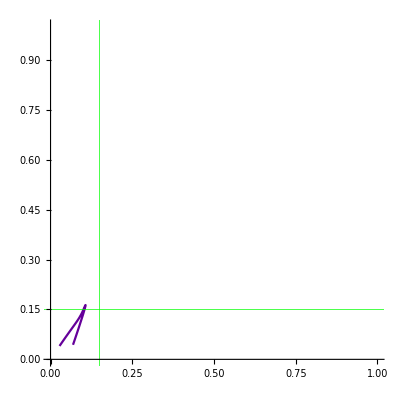

{0.0275425,0.0402194}

```mathematica
{x10,x20,y10,y20}={0.06875000,0.04375000,0.05416667,0.09583333};
tMax=3600;
numericalIntegration =NDSolve[{
Subscript[x, 1]'[t]==(1-Subscript[x, 1][t])(1-κ Subscript[u, 1])(Subscript[b, 11] Subscript[y, 1][t]+Subscript[b, 12] Subscript[y, 2][t]) - Subscript[γ, 1] Subscript[x, 1][t],
Subscript[x, 2]'[t]==(1-Subscript[x, 2][t])(1-κ Subscript[u, 2])(Subscript[b, 21] Subscript[y, 1][t]+Subscript[b, 22] Subscript[y, 2][t]) - Subscript[γ, 2] Subscript[x, 2][t],
Subscript[y, 1]'[t]==(1-Subscript[y, 1][t])(Subscript[c, 11](1-κ Subscript[u, 1])Subscript[x, 1][t]+Subscript[c, 12](1-κ Subscript[u, 2])Subscript[x, 2][t]) - Subscript[μ, 1] Subscript[y, 1][t],
Subscript[y, 2]'[t]==(1-Subscript[y, 2][t])(Subscript[c, 21](1-κ Subscript[u, 1])Subscript[x, 1][t]+Subscript[c, 22](1-κ Subscript[u, 2])Subscript[x, 2][t]) - Subscript[μ, 2] Subscript[y, 2][t],
Subscript[x, 1][0]==x10,Subscript[x, 2][0]==x20,Subscript[y, 1][0]==y10,Subscript[y, 2][0]==y20},
{Subscript[x, 1],Subscript[x, 2],Subscript[y, 1],Subscript[y, 2]},
{t,0,tMax}
];
{botswana,zimbabwe}={Subscript[x, 1],Subscript[x, 2]}/.numericalIntegration⟦1⟧;
solutionPlot=ParametricPlot[{botswana[t],zimbabwe[t]},{t,0,tMax},PlotRange->{{0,1},{0,1}},GridLines->{{Subscript[Imax, 1]},{Subscript[Imax, 2]}},GridLinesStyle->Directive[Green,Thick],ColorFunction->Function[{x,y,tscaled},Blend[{Red,Blue},Power[tscaled, 0.3]]]];
Show[{solutionPlot}]
{botswana[tMax], zimbabwe[tMax]}
```

```mathematica
humanSolutions = ({#⟦1⟧,#⟦2⟧,{Subscript[x, 1],Subscript[x, 2]}/.(#⟦3⟧⟦1⟧)}&)/@equilibriumPoints;
botswanaNormalized = ({#⟦1⟧,#⟦2⟧,#⟦3⟧⟦1⟧}&)/@humanSolutions;
zimbabweNormalized = ({#⟦1⟧,#⟦2⟧,#⟦3⟧⟦2⟧}&)/@humanSolutions;
```

```mathematica
(* YES 0.05000000,0.00833333,0.06875000,0.06875000,  *)
(* YES 0.05000000,0.04375000,0.07083333,0.02083333, -8.15115601e-08 *)
(* NO 0.05000000,0.04375000,0.06666667,0.09583333, -7.15743167e-08 *)
(* NO 0.08125000,0.10625000,0.05000000,0.07500000, -5.43740266e-08 *)
(* YES 0.14375000,0.01250000,-0.00833333,0.00000000, -8.44697592e-08 *)
(* NO 0.10625000,0.13750000,0.11666667,0.05000000, -4.75063590e-10 *)
(* YES 0.06875000,0.04375000,0.05416667,0.02916667, -7.70061768e-10 *)
(* NO 0.06875000,0.04375000,0.05416667,0.09583333, -6.85949469e-10 *)
```